Hatano-Nelson Model: Monte Carlo Simulation |

The Modelpaclet:QuantumMob/QuantumPlaybook/tutorial/HatanoNelsonModel#1347436005 | Monte Carlo Simulation: Projective Modelpaclet:QuantumMob/QuantumPlaybook/tutorial/HatanoNelsonModel#282738307
Monte Carlo Simulation: Dissipative Modelpaclet:QuantumMob/QuantumPlaybook/tutorial/HatanoNelsonModel#1966157191 |

The Hatano-Nelson model is a non-Hermitian Hamiltonian model of fermionic modes exhibiting the so-called skin effect. It was introduced by  Hatano and Nelson in 1996, originally, in the context of localization transitions, and later applied to describe vortex pinning in superconductors (Hatano and Nelson, 1997). The non-hermicity and associated skin effect come from quantum dissipative processes through a coupling to the bath (Kawabata, Numasawa and Ryu, 2023).

This tutorial presents a simulation of the quantum master equation of the Hatano-Nelson model.

WickStatepaclet:QuantumMob/Q3/ref/WickStateQuantumMob Package Symbol | Represents a fermionic Gaussian state.
WickNonunitarypaclet:QuantumMob/Q3/ref/WickNonunitaryQuantumMob Package Symbol | Represents a non-unitary evolution operator associated with local quadratic non-Hermitian Hamiltonian
WickJumppaclet:QuantumMob/Q3/ref/WickJumpQuantumMob Package Symbol | Represents a set of quantum jump operators
WickSimulatepaclet:QuantumMob/Q3/ref/WickSimulateQuantumMob Package Symbol | Simulates the quantum master equation for a dissipative fermionic system

Q3 functions for the Monte Carlo simulation of open quantum systems of non-interacting fermions.

The Model

Make sure that Q3 is loaded.

```mathematica
Needs["QuantumMob`Q3`"]
```

Set the number of fermion modes to consider.

```mathematica
$L=6;
```

Although unnecessary for simulation itself in the below, here we need to choose a specific set of fermion modes to examine the model.

```mathematica
Let[Fermion,c]
cc=c[Range@$L]
```

{c_(,,1),c_(,,2),c_(,,3),c_(,,4),c_(,,5),c_(,,6)}

We consider auxiliary fermion modes for convenience. They will be used mainly to describe the quantum jump operators.

```mathematica
Let[Fermion,a,b]
aa=a[Range[$L-1]]
bb=b[Range[$L-1]]
```

{a_(,,1),a_(,,2),a_(,,3),a_(,,4),a_(,,5)}

{b_(,,1),b_(,,2),b_(,,3),b_(,,4),b_(,,5)}

The hopping amplitude.

```mathematica
Let[Real,J]
```

The single-particle Hamiltonian.

```mathematica
hamOp=-J*Hop[cc]//PlusDagger
ham=CoefficientTensor[hamOp,Dagger@cc,cc];
ham//ArrayShort
```

-J (c_(,,1)^(,,†)c_(,,2)+c_(,,2)^(,,†)c_(,,3)+c_(,,3)^(,,†)c_(,,4)+c_(,,4)^(,,†)c_(,,5)+c_(,,5)^(,,†)c_(,,6))-J (c_(,,2)^(,,†)c_(,,1)+c_(,,3)^(,,†)c_(,,2)+c_(,,4)^(,,†)c_(,,3)+c_(,,5)^(,,†)c_(,,4)+c_(,,6)^(,,†)c_(,,5))

(0 | -J | 0 | 0 | …
-J | 0 | -J | 0 | …
0 | -J | 0 | -J | …
0 | 0 | -J | 0 | …
… | … | … | … | …)

### Dissipative Model

Construct the quantum jump operators.

```mathematica
a[k_]:=(c[k]+I*c[k+1])/Sqrt[2]
b[k_]:=(c[k]-I*c[k+1])/Sqrt[2]
ab=Join[aa,Dagger@bb];
ab//TableForm
```

(c_(,,1)+ⅈ c_(,,2))/(√2)
(c_(,,2)+ⅈ c_(,,3))/(√2)
(c_(,,3)+ⅈ c_(,,4))/(√2)
(c_(,,4)+ⅈ c_(,,5))/(√2)
(c_(,,5)+ⅈ c_(,,6))/(√2)
(c_(,,1)^(,,†)+ⅈ c_(,,2)^(,,†))/(√2)
(c_(,,2)^(,,†)+ⅈ c_(,,3)^(,,†))/(√2)
(c_(,,3)^(,,†)+ⅈ c_(,,4)^(,,†))/(√2)
(c_(,,4)^(,,†)+ⅈ c_(,,5)^(,,†))/(√2)
(c_(,,5)^(,,†)+ⅈ c_(,,6)^(,,†))/(√2)

Construct the effective non-Hermitian Hamiltonian, which results in the so-called  Hatano-Nelson model.

```mathematica
dmpOp=γ*Total[Dagger[ab]**ab]//Garner
```

5 γ+ⅈ γ c_(,,1)^(,,†)c_(,,2)-ⅈ γ c_(,,2)^(,,†)c_(,,1)+ⅈ γ c_(,,2)^(,,†)c_(,,3)-ⅈ γ c_(,,3)^(,,†)c_(,,2)+ⅈ γ c_(,,3)^(,,†)c_(,,4)-ⅈ γ c_(,,4)^(,,†)c_(,,3)+ⅈ γ c_(,,4)^(,,†)c_(,,5)-ⅈ γ c_(,,5)^(,,†)c_(,,4)+ⅈ γ c_(,,5)^(,,†)c_(,,6)-ⅈ γ c_(,,6)^(,,†)c_(,,5)

```mathematica
nonOp=hamOp-I*dmpOp//Garner
```

-5 ⅈ γ+(-J+γ) c_(,,1)^(,,†)c_(,,2)+(-J-γ) c_(,,2)^(,,†)c_(,,1)+(-J+γ) c_(,,2)^(,,†)c_(,,3)+(-J-γ) c_(,,3)^(,,†)c_(,,2)+(-J+γ) c_(,,3)^(,,†)c_(,,4)+(-J-γ) c_(,,4)^(,,†)c_(,,3)+(-J+γ) c_(,,4)^(,,†)c_(,,5)+(-J-γ) c_(,,5)^(,,†)c_(,,4)+(-J+γ) c_(,,5)^(,,†)c_(,,6)+(-J-γ) c_(,,6)^(,,†)c_(,,5)

```mathematica
non=CoefficientTensor[nonOp,Dagger@cc,cc];
-non//ArrayShort
```

(0 | J-γ | 0 | 0 | …
J+γ | 0 | J-γ | 0 | …
0 | J+γ | 0 | J-γ | …
0 | 0 | J+γ | 0 | …
… | … | … | … | …)

### Projective Model

Another choice of quantum jump operators that leads to the same Hatano-Nelson Hamiltonian is the projection operators L_(2k-1):=a_k^†a_k and L_(2k):=b_k b_k^†, where a_k and b_k are the auxiliary fermion modes defined above.

```mathematica
prj=Dagger[ab]**ab
```

{1/2 c_(,,1)^(,,†)c_(,,1)+1/2 ⅈ c_(,,1)^(,,†)c_(,,2)-1/2 ⅈ c_(,,2)^(,,†)c_(,,1)+1/2 c_(,,2)^(,,†)c_(,,2),1/2 c_(,,2)^(,,†)c_(,,2)+1/2 ⅈ c_(,,2)^(,,†)c_(,,3)-1/2 ⅈ c_(,,3)^(,,†)c_(,,2)+1/2 c_(,,3)^(,,†)c_(,,3),1/2 c_(,,3)^(,,†)c_(,,3)+1/2 ⅈ c_(,,3)^(,,†)c_(,,4)-1/2 ⅈ c_(,,4)^(,,†)c_(,,3)+1/2 c_(,,4)^(,,†)c_(,,4),1/2 c_(,,4)^(,,†)c_(,,4)+1/2 ⅈ c_(,,4)^(,,†)c_(,,5)-1/2 ⅈ c_(,,5)^(,,†)c_(,,4)+1/2 c_(,,5)^(,,†)c_(,,5),1/2 c_(,,5)^(,,†)c_(,,5)+1/2 ⅈ c_(,,5)^(,,†)c_(,,6)-1/2 ⅈ c_(,,6)^(,,†)c_(,,5)+1/2 c_(,,6)^(,,†)c_(,,6),1-1/2 c_(,,1)^(,,†)c_(,,1)+1/2 ⅈ c_(,,1)^(,,†)c_(,,2)-1/2 ⅈ c_(,,2)^(,,†)c_(,,1)-1/2 c_(,,2)^(,,†)c_(,,2),1-1/2 c_(,,2)^(,,†)c_(,,2)+1/2 ⅈ c_(,,2)^(,,†)c_(,,3)-1/2 ⅈ c_(,,3)^(,,†)c_(,,2)-1/2 c_(,,3)^(,,†)c_(,,3),1-1/2 c_(,,3)^(,,†)c_(,,3)+1/2 ⅈ c_(,,3)^(,,†)c_(,,4)-1/2 ⅈ c_(,,4)^(,,†)c_(,,3)-1/2 c_(,,4)^(,,†)c_(,,4),1-1/2 c_(,,4)^(,,†)c_(,,4)+1/2 ⅈ c_(,,4)^(,,†)c_(,,5)-1/2 ⅈ c_(,,5)^(,,†)c_(,,4)-1/2 c_(,,5)^(,,†)c_(,,5),1-1/2 c_(,,5)^(,,†)c_(,,5)+1/2 ⅈ c_(,,5)^(,,†)c_(,,6)-1/2 ⅈ c_(,,6)^(,,†)c_(,,5)-1/2 c_(,,6)^(,,†)c_(,,6)}

Since a_k^†a_k and b_k b_k^† are projection operators, it is clear that they reproduces the same effective damping operator; Σ_μ L_μ^†L_μ=Σ_k a_k^†a_k+Σ_k b_k^†b_k=2G.

```mathematica
dmpOp=γ*Total[prj]
```

γ (5+ⅈ c_(,,1)^(,,†)c_(,,2)-ⅈ c_(,,2)^(,,†)c_(,,1)+ⅈ c_(,,2)^(,,†)c_(,,3)-ⅈ c_(,,3)^(,,†)c_(,,2)+ⅈ c_(,,3)^(,,†)c_(,,4)-ⅈ c_(,,4)^(,,†)c_(,,3)+ⅈ c_(,,4)^(,,†)c_(,,5)-ⅈ c_(,,5)^(,,†)c_(,,4)+ⅈ c_(,,5)^(,,†)c_(,,6)-ⅈ c_(,,6)^(,,†)c_(,,5))

Monte Carlo Simulation: Dissipative Model

### Setting Up the Model

Here, we construct the model without referring to any specific set of fermion modes.

Make sure that Q3 is loaded:

```mathematica
Needs["QuantumMob`Q3`"]
```

Set the number of fermion modes:

```mathematica
$L=6;
```

Construct the single-particle Hamiltonian matrix:

```mathematica
$J=2;
```

```mathematica
ham=PlusTopple[-$J*One[{$L,$L},1]];
ham=WickHermitian[ham]
ham//ArrayShort
```

WickHermitian[…]

(0 | -2 | 0 | 0 | …
-2 | 0 | -2 | 0 | …
0 | -2 | 0 | -2 | …
0 | 0 | -2 | 0 | …
… | … | … | … | …)

Construct the quantum jump operators. (Note that we choose a unit system such that γ=1:

```mathematica
cff=One[{$L-1,$L}]+I*One[{$L-1,$L},1];
cff//MatrixForm
```

(1 | ⅈ | 0 | 0 | 0 | 0
0 | 1 | ⅈ | 0 | 0 | 0
0 | 0 | 1 | ⅈ | 0 | 0
0 | 0 | 0 | 1 | ⅈ | 0
0 | 0 | 0 | 0 | 1 | ⅈ)

```mathematica
jmp=WickJump@Join[
Thread[cff/Sqrt[2]->0],
Thread[Conjugate@cff/Sqrt[2]->1]
];
First[jmp]//Normal//TableForm
```

{1/(√2),ⅈ/(√2),0,0,0,0}→0
{0,1/(√2),ⅈ/(√2),0,0,0}→0
{0,0,1/(√2),ⅈ/(√2),0,0}→0
{0,0,0,1/(√2),ⅈ/(√2),0}→0
{0,0,0,0,1/(√2),ⅈ/(√2)}→0
{1/(√2),-ⅈ/(√2),0,0,0,0}→1
{0,1/(√2),-ⅈ/(√2),0,0,0}→1
{0,0,1/(√2),-ⅈ/(√2),0,0}→1
{0,0,0,1/(√2),-ⅈ/(√2),0}→1
{0,0,0,0,1/(√2),-ⅈ/(√2)}→1

Check the effective non-Hermitian Hamiltonian (for a single-particle):

```mathematica
{dmp,gmm}=WickDampingOperator[jmp];
eff=ham-I*dmp;
eff//ArrayShort
```

(0 | -3/2 | 0 | 0 | …
-5/2 | 0 | -3/2 | 0 | …
0 | -5/2 | 0 | -3/2 | …
0 | 0 | -5/2 | 0 | …
… | … | … | … | …)

### Monte Carlo Simulation

Let us now perform the Monte-Carlo simulation on the Hatano-Nelson model.

Pick an initial state with half filling:

```mathematica
in=WickState[{1,0},$L]
```

WickState[…]

To reproduce exactly the same simulation results, seed the random processor:

```mathematica
SeedRandom[450];
```

Do the simulation.

```mathematica
EchoTiming[
data=WickSimulate[in,ham,jmp,{$T=10,$dt=0.025},
"Samples"->100]
];
```

14.317

Check some basic things about the data:

```mathematica
Dimensions[data]
```

{100,401}

```mathematica
data[[1,3]]
```

WickState[…]

### Entanglement Properties

Choose a subsystem:

```mathematica
sub=Range[$L/2]
```

{1,2,3}

Calculate the entanglement entropy (EE) between the subsystem and the rest:

```mathematica
EchoTiming[
ee=Mean@WickEntanglementEntropy[data,sub]
];
Dimensions[ee]
```

1.54051

{401}

Check the entanglement entropy as a function of time:

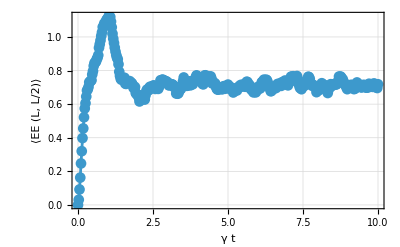

```mathematica
ListLinePlot[Re[ee],
DataRange->{0,$T},
PlotRange->All,
PlotMarkers->Automatic,
FrameLabel->{"γ t","⟨EE (L, L/2)⟩"}
]
```

Calculate the mutual information (MI) between the subsystem and the rest:

```mathematica
EchoTiming[
mi=Mean@WickMutualInformation[data,sub]
];
```

3.91444

Check the mutual information as a function of time.

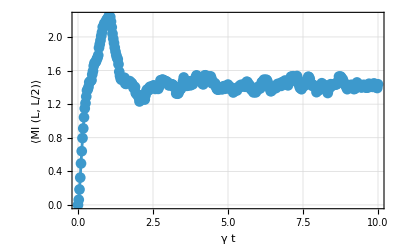

```mathematica
ListLinePlot[Re[mi],
DataRange->{0,$T},
PlotRange->All,
PlotMarkers->Automatic,
FrameLabel->{"γ t","⟨MI (L, L/2)⟩"}
]
```

Calculate the logarithmic negativity (LN) between the subsystem and the rest:

```mathematica
EchoTiming[
neg=Mean@WickLogarithmicNegativity[data,sub]
];
```

3.58988

Check the logarithmic negativity as a function of time:

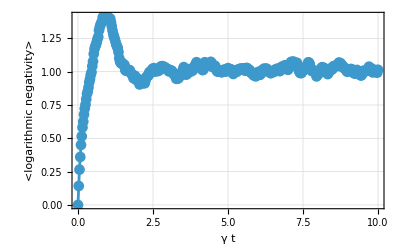

```mathematica
ListLinePlot[Re[neg],
DataRange->{0,$T},
PlotRange->All,
PlotMarkers->Automatic,
FrameLabel->{"γ t","<logarithmic negativity>"}
]
```

Construct approximate density matrices by taking averages of the covariance matrices in different trajectories, and calculate the logarithmic negativity (LN) between the subsystem and the rest in the density matrices:

```mathematica
EchoTiming[
avg=Mean@WickGreen[data];
negRho=WickLogarithmicNegativity[avg,sub]
];
```

0.768212

Check the logarithmic negativity as a function of time:

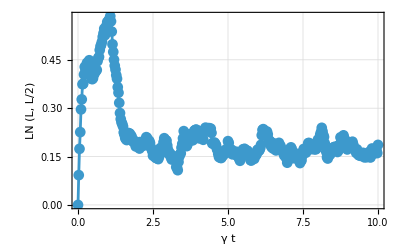

```mathematica
ListLinePlot[Re@negRho,
DataRange->{0,$T},
PlotRange->All,
PlotMarkers->Automatic,
FrameLabel->{"γ t","LN (L, L/2)"}
]
```

Monte Carlo Simulation: Projective Model

Let us now consider the projective model for the Hatano-Nelson Hamiltonian. In this case, each quantum jump operators are projection operators, and the problem can be regarded as a continuous monitoring of the dressed fermion modes.

### Setting Up the Model

Make sure that Q3 is loaded:

```mathematica
Needs["QuantumMob`Q3`"]
```

Set the number of fermion modes:

```mathematica
$L=6;
```

Construct the single-particle Hamiltonian matrix:

```mathematica
$J=2;
```

```mathematica
mat=PlusTopple[-$J*One[{$L,$L},1]];
ham=WickHermitian[mat]
```

WickHermitian[…]

Construct the quantum jump operators,  this time, using  WickMeasurementpaclet:QuantumMob/Q3/ref/WickMeasurementQuantumMob Package Symbol instead of WickJumppaclet:QuantumMob/Q3/ref/WickJumpQuantumMob Package Symbol:

```mathematica
cff=One[{$L-1,$L}]+I*One[{$L-1,$L},1];
cff=Join[cff,Conjugate@cff];
msr=WickMeasurement[Normalize/@cff]
msr//MatrixForm
```

WickMeasurement[…]

(1/(√2) | ⅈ/(√2) | 0 | 0 | 0 | 0
0 | 1/(√2) | ⅈ/(√2) | 0 | 0 | 0
0 | 0 | 1/(√2) | ⅈ/(√2) | 0 | 0
0 | 0 | 0 | 1/(√2) | ⅈ/(√2) | 0
0 | 0 | 0 | 0 | 1/(√2) | ⅈ/(√2)
1/(√2) | -ⅈ/(√2) | 0 | 0 | 0 | 0
0 | 1/(√2) | -ⅈ/(√2) | 0 | 0 | 0
0 | 0 | 1/(√2) | -ⅈ/(√2) | 0 | 0
0 | 0 | 0 | 1/(√2) | -ⅈ/(√2) | 0
0 | 0 | 0 | 0 | 1/(√2) | -ⅈ/(√2))

### Monte Carlo Simulation

Let us now perform the Monte-Carlo simulation on the projective model for Hatano-Nelson Hamiltonian.

Pick an initial state with half filling:

```mathematica
in=WickState[{1,0},$L]
```

WickState[…]

Do the simulation:

```mathematica
SeedRandom[450];
```

```mathematica
EchoTiming[
data=WickMonitor[in,ham,msr,{$T=10,$dt=0.025},
"Samples"->100]
];
Dimensions[data]
```

5.8773

{100,401}

### Entanglement Properties

Choose a subsystem:

```mathematica
sub=Range[$L/2]
```

{1,2,3}

Calculate the entanglement entropy (EE) between the subsystem and the rest:

```mathematica
EchoTiming[
ee=Mean@WickEntanglementEntropy[data,sub]
];
Dimensions[ee]
```

1.78886

{401}

Check the entanglement entropy as a function of time:

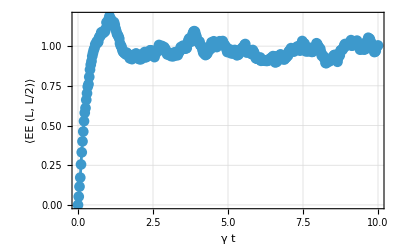

```mathematica
ListLinePlot[Re[ee],
DataRange->{0,$T},
PlotMarkers->Automatic,
FrameLabel->{"γ t","⟨EE (L, L/2)⟩"}
]
```

Calculate the mutual information (MI) between the subsystem and the rest:

```mathematica
EchoTiming[
mi=Mean@WickMutualInformation[data,sub]
];
```

4.1188

Plot the mutual information as a function of time:

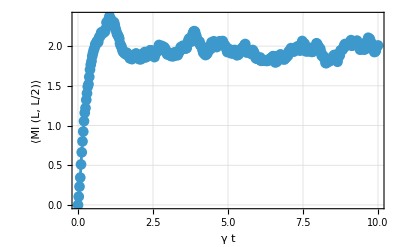

```mathematica
ListLinePlot[Re[mi],
DataRange->{0,$T},
PlotMarkers->Automatic,
FrameLabel->{"γ t","⟨MI (L, L/2)⟩"}
]
```

Calculate the logarithmic negativity (LN) between the subsystem and the rest:

```mathematica
EchoTiming[
neg=Mean@WickLogarithmicNegativity[data,sub]
];
```

General::munfl: (9.28207×10^-279)^2 is too small to represent as a normalized machine number; precision may be lost.

3.62346

Plot the logarithmic negativity as a function of time:

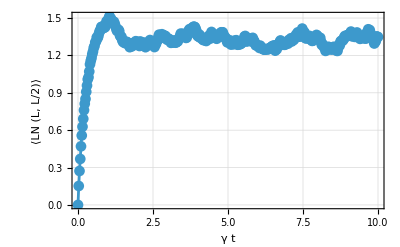

```mathematica
ListLinePlot[Re[neg],
DataRange->{0,$T},
PlotMarkers->Automatic,
FrameLabel->{"γ t","⟨LN (L, L/2)⟩"}
]
```

Construct approximate density matrices by taking averages of the covariance matrices in different trajectories, and calculate the logarithmic negativity (LN) between the subsystem and the rest in the density matrices:

```mathematica
EchoTiming[
avg=Mean@WickGreen[data];
negRho=WickLogarithmicNegativity[avg,sub]
];
```

0.760038

Check the logarithmic negativity as a function of time:

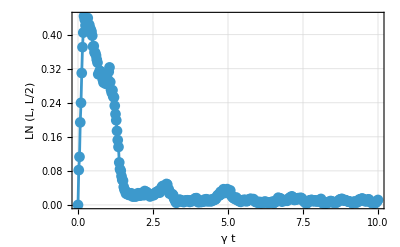

```mathematica
ListLinePlot[Re@negRho,
DataRange->{0,$T},
PlotMarkers->Automatic,
PlotRange->All,
FrameLabel->{"γ t","LN (L, L/2)"}
]
```

| Related Guides
▪Fermionic Quantum Computation
▪Quantum Many-Body Systems
▪Q3

| Related Tech Notes
▪Majorana Fermions
▪A Quantum Playbook
▪Quantum Many-Body Systems with Q3
▪Q3: Quick Start

| Related Links
▪K. Kawabata, T. Numasawa and S. Ryu (2023)https://doi.org/10.1103/PhysRevX.13.021007, Physical Review X 13, 021007, "Entanglement Phase Transition Induced by the Non-Hermitian Skin Effect."
▪X. https://doi.org/10.1103/PhysRevB.110.144305Feng and S. Chen (2024)https://doi.org/10.1103/PhysRevB.110.144305, Physical Review B 110, 144305, "Delocalization of skin steady states."
▪N. Hatano and D. R. Nelson (1996)https://doi.org/10.1103/PhysRevLett.77.570, Physical Review Letters 77, 570, "Localization Transitions in Non-Hermitian Quantum Mechanics."
▪N. Hatano and D. R. Nelson (1997)https://doi.org/10.1103/PhysRevB.56.8651, Physical Review B 56, 287, "Vortex Pinning and Non-Hermitian Quantum Mechanics."
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).